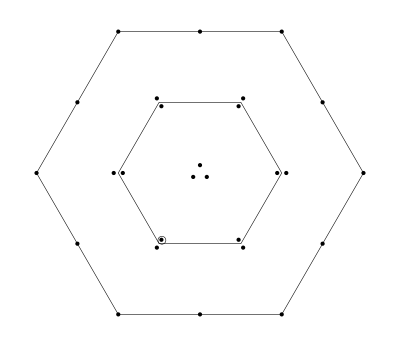

Y=-1.5,  I_3=-0.5

2(sd+ds)(ūd̄+d̄ū)-ss(ūs̄+s̄ū)-(us+su)ūū

```mathematica
(*-------------------------------*)
```

The current J:

2 (d_a^T C γ^μ s_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+2 (s_a^T C γ^μ d_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+2 (d_a^T C γ^μ s_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+2 (s_a^T C γ^μ d_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+(s_a^T C γ^μ s_b) ((s̄)_a γ^μ C((ū)_b)^T-(s̄)_b γ^μ C((ū)_a)^T)+(s_a^T C γ^μ s_b) ((ū)_a γ^μ C((s̄)_b)^T-(ū)_b γ^μ C((s̄)_a)^T)+((ū)_a γ^μ C((ū)_b)^T-(ū)_b γ^μ C((ū)_a)^T) (s_a^T C γ^μ u_b)+((ū)_a γ^μ C((ū)_b)^T-(ū)_b γ^μ C((ū)_a)^T) (u_a^T C γ^μ s_b)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
4 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 s)+4 (d̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 d)-4 (d̄ γ^μ d ū γ^μ s)-4 (d̄ γ^μ s ū γ^μ d)+4 (2 (d̄(γ̄)^5 d)-s̄(γ̄)^5 s) (ū(γ̄)^5 s)+8 (d̄(γ̄)^5 s ū(γ̄)^5 d)+4 (s̄ 1s-2 (d̄ 1d)) (ū 1s)-8 (d̄ 1s ū 1d)-2 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 s)+2 (s̄ γ^μ s ū γ^μ s)-2 (ū(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)+2 (ū γ^μ s ū γ^μ u)-4 (ū(γ̄)^5 s ū(γ̄)^5 u)+4 (ū 1s ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(192 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(48 π^5)+(⟨ ū u⟩ log(-q^2/μ^2) (4 m_d+m_s-5 m_u) q^4)/(6 π^4)-(2 ⟨ d̄ d⟩ log(-q^2/μ^2) (2 m_d-m_s-m_u) q^4)/(3 π^4)+(⟨ s̄ s⟩ log(-q^2/μ^2) (4 m_d-5 m_s+m_u) q^4)/(6 π^4)-(32 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(10 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(10 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(125 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(864 π^6)+(16 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(16 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(20 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(4 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(4 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(4 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(4 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(32 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(7 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(9 π q^2)-(7 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-(11 ⟨ s̄ Gs⟩^2)/(192 π^2 q^2)-(11 ⟨ ū Gu⟩^2)/(192 π^2 q^2)+(40 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)+(40 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)-(14 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)-(11 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(24 π^2 q^2)-(11 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(24 π^2 q^2)-(11 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(96 π^2 q^2)-(64 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (m_d+2 m_s))/(9 q^2)+(128 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_s+m_u))/(9 q^2)-(64 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (m_d+2 m_u))/(9 q^2)+(128 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (m_s+2 m_u))/(9 q^2)-(8 ⟨ s̄ s⟩^3 (5 m_s+4 m_u))/(9 q^2)-(8 ⟨ ū u⟩^3 (4 m_s+5 m_u))/(9 q^2)-(8 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (21 m_s+6 m_u))/(9 q^2)-(8 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (6 m_s+21 m_u))/(9 q^2)+(64 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (8 m_d+5 (m_s+m_u)))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

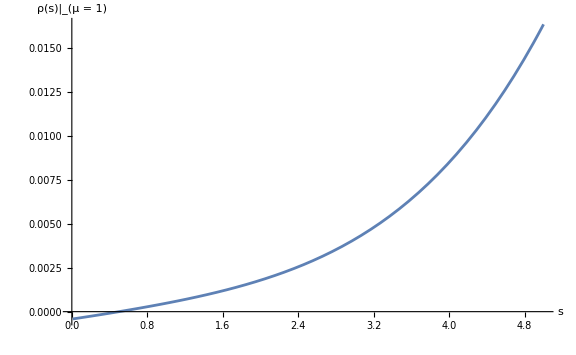
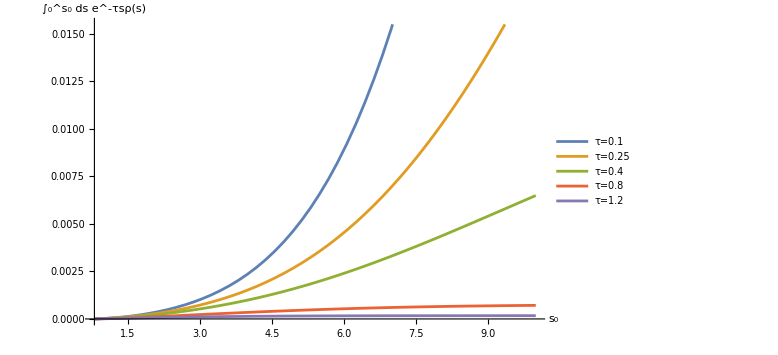

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

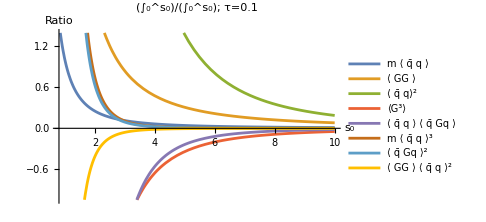
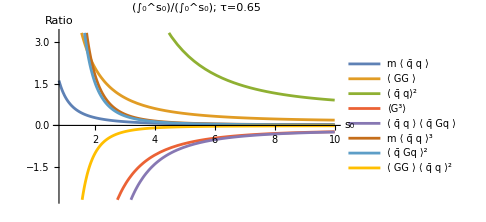
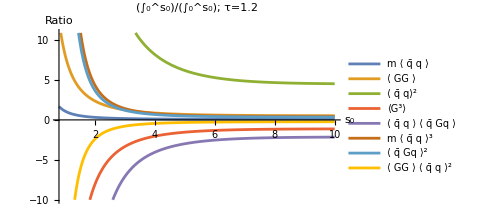

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

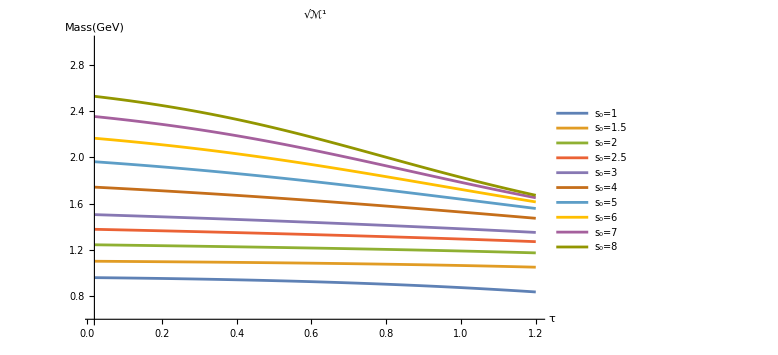
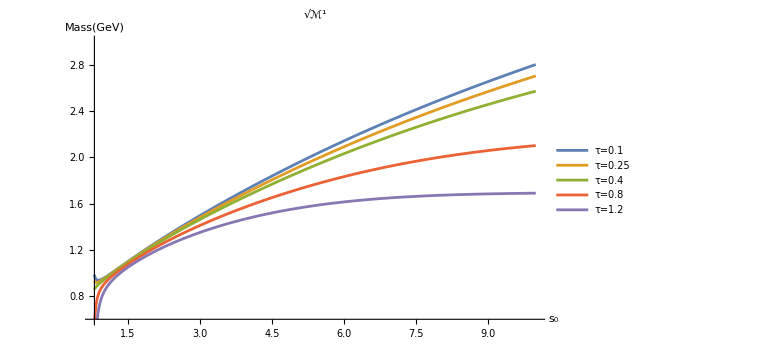

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

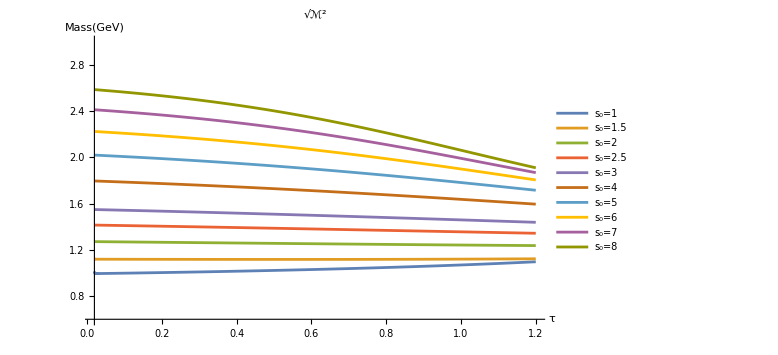
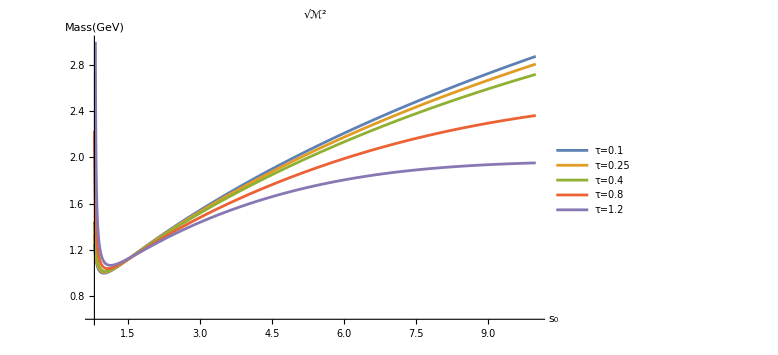

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

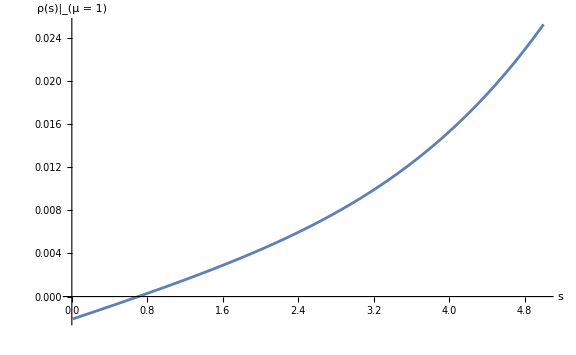
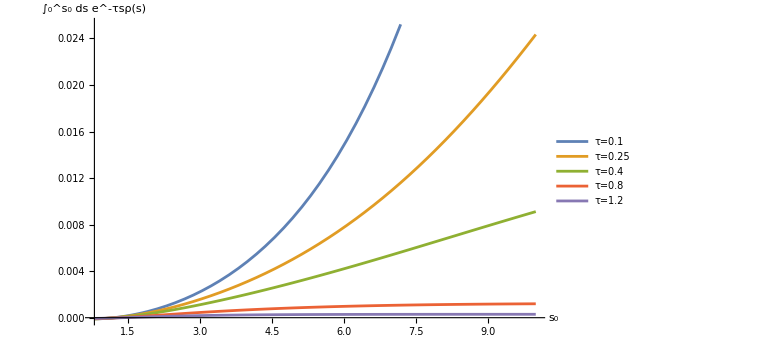

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

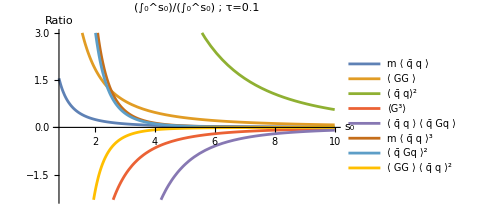
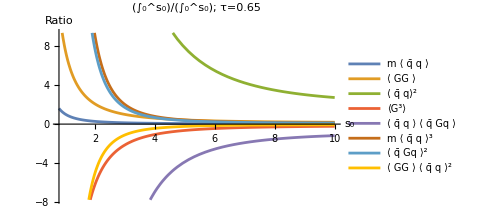
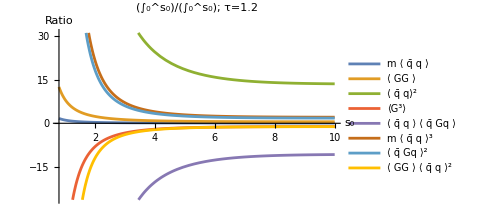

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

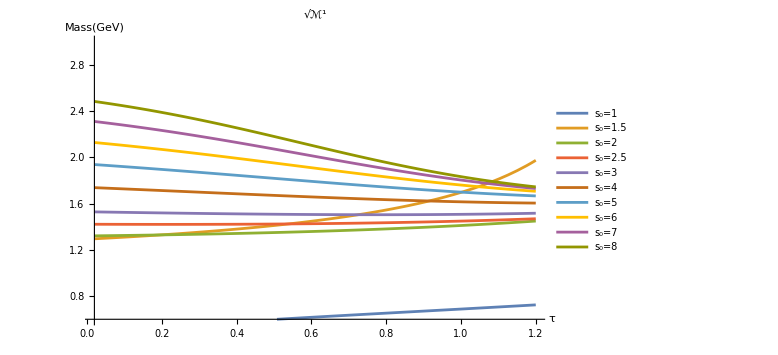
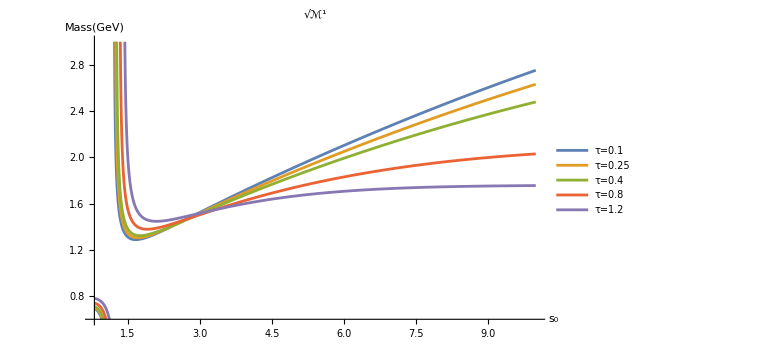

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5